```mathematica
Remove["Global`*"];
Off[General::Spell1];
ClearAll["Global `*"];
```

```mathematica
(*Factorizar el número M=15*)
M=15;
(*x es el número por el que se multiplicará en el algoritmo*)
(*x=RandomInteger[{2,M-2}]*)
GCD[x,M]==1
x=7
```

GCD[15,x]==1

7

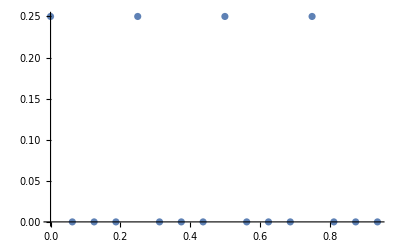

```mathematica
(*Los |0> y |1>*)
Subscript[ket, 0]={{1},{0}};
Subscript[ket, 1]={{0},{1}};

(*El operador identidad*)
Id=IdentityMatrix[2];

(*Las matrices de Pauli*)
X=PauliMatrix[1];
Y=PauliMatrix[2];
Z=PauliMatrix[3];

(*La compuerta de Hadamard*)
H=HadamardMatrix[2];

(*Los proyectores de la base computacional*)
Subscript[P, 0]=Subscript[ket, 0].ConjugateTranspose[Subscript[ket, 0]];
Subscript[P, 1]=Subscript[ket, 1].ConjugateTranspose[Subscript[ket, 1]];

(*Operador de cambio de fase*)
R[ϕ_]:=Subscript[P, 0] + ⅇ^(ⅈ ϕ) Subscript[P, 1];

(*Compuertas condicionales*)
CNOT=KroneckerProduct[Subscript[P, 0],Id]+KroneckerProduct[Subscript[P, 1],X];
CR[ϕ_]:=KroneckerProduct[Subscript[P, 0],Id]+KroneckerProduct[Subscript[P, 1],R[ϕ]];
CR13[ϕ_]:=KroneckerProduct[Subscript[P, 0],Id,Id]+KroneckerProduct[Subscript[P, 1],Id,R[ϕ]];

(*Ket general de la base computacional de dimensión 16*)
ket[n_]:=Table[{n==i-1},{i,1,16}]/.{True->1,False->0};

(*Operador de multiplicación módulo*)
Urp[x_,N_]:=Sum[ket[Mod[x i,N]].ConjugateTranspose[ket[i]],{i,0,N-1}]+Sum[ket[i].ConjugateTranspose[ket[i]],{i,N,15}];

(*Matriz de densidad*)
ρ[ψ_]:=ψ.ConjugateTranspose[ψ];

(*Operador para la estimación de fase: Operador de multiplicación por 7 módulo 15*)
U=Urp[x,M];

(*Preparando el estado inicial*)
ψ0=KroneckerProduct[Subscript[ket, 0],Subscript[ket, 0],Subscript[ket, 0],Subscript[ket, 0]];
ψ0=KroneckerProduct[H,H,H,H].ψ0;
ψ=KroneckerProduct[Subscript[ket, 0],Subscript[ket, 0],Subscript[ket, 0],Subscript[ket, 1]];

ψt=KroneckerProduct[ψ0,ψ];

(*Estimación de fase*)
ψt=(KroneckerProduct[Id,Id,Id,Subscript[P, 0],Id,Id,Id,Id]+KroneckerProduct[Id,Id,Id,Subscript[P, 1],U]).ψt;
ψt=(KroneckerProduct[Id,Id,Subscript[P, 0],Id,Id,Id,Id,Id]+KroneckerProduct[Id,Id,Subscript[P, 1],Id,MatrixPower[U,2]]).ψt;
ψt=(KroneckerProduct[Id,Subscript[P, 0],Id,Id,Id,Id,Id,Id]+KroneckerProduct[Id,Subscript[P, 1],Id,Id,MatrixPower[U,2^2]]).ψt;
ψt=(KroneckerProduct[Subscript[P, 0],Id,Id,Id,Id,Id,Id,Id]+KroneckerProduct[Subscript[P, 1],Id,Id,Id,MatrixPower[U,2^3]]).ψt;

(*QFT^-1*)
ψt=KroneckerProduct[ConjugateTranspose[FourierMatrix[2^4]],Id,Id,Id,Id].ψt;

(*Medidas*)
For[i=0,i<16,i++,sub0=Mod[i,2];sub1=Which[i==0,0,Mod[i,2]==0&&sub1==0,1,Mod[i,2]==0&&sub1==1,0,True,sub1];sub2=Which[i==0,0,Mod[i,2^2]==0&&sub2==0,1,Mod[i,2^2]==0&&sub2==1,0,True,sub2];sub3=Which[i==0,0,Mod[i,2^3]==0&&sub3==0,1,Mod[i,2^3]==0&&sub3==1,0,True,sub3];Subscript[ψt, i]=KroneckerProduct[Subscript[P, sub3],Subscript[P, sub2],Subscript[P, sub1],Subscript[P, sub0],Id,Id,Id,Id].ψt;Subscript[ψt, i]=ConjugateTranspose[Subscript[ψt, i]].Subscript[ψt, i];]

(*Organizar resultados de las medidas y graficar*)
L=Table[{i,i/2^4,Subscript[ψt, i][[1,1]]},{i,0,15}];
ListPlot[Table[{i/2^4,Subscript[ψt, i][[1,1]]},{i,0,15}],PlotRange->All]
```

```mathematica
L//FullSimplify
Lpypart15={0.18265120316248348,0.030148605498127055,0.0117556126084082,0.027068348030583445,0.17700021614033762,0.028491802773181096,0.011881438650927171,0.028510782606300467,0.17917422966710292,0.029450553218688075,0.012081135256705483,0.027710388875941253,0.18489803932544116,0.02936951642045106,0.012035158723792341,0.027772969041529337}
Lpy=Table[{i,i/2^4,Lpypart15[[i+1]]},{i,0,15}];
Table[L[[i,3]] Lpy[[i,3]],{i,1,16}]//FullSimplify
Sum[√(L[[i,3]] Lpy[[i,3]]),{i,1,16}]//FullSimplify
```

{{0,0,1/4},{1,1/16,0},{2,1/8,0},{3,3/16,0},{4,1/4,1/4},{5,5/16,0},{6,3/8,0},{7,7/16,0},{8,1/2,1/4},{9,9/16,0},{10,5/8,0},{11,11/16,0},{12,3/4,1/4},{13,13/16,0},{14,7/8,0},{15,15/16,0}}

{0.182651,0.0301486,0.0117556,0.0270683,0.177,0.0284918,0.0118814,0.0285108,0.179174,0.0294506,0.0120811,0.0277104,0.184898,0.0293695,0.0120352,0.027773}

{0.0456628,5.80641×10^-36+0. ⅈ,9.05619×10^-36+0. ⅈ,5.21317×10^-36+0. ⅈ,0.0442501,5.48732×10^-36+0. ⅈ,9.15313×10^-36+0. ⅈ,5.49098×10^-36+0. ⅈ,0.0447936,5.67197×10^-36+0. ⅈ,9.30697×10^-36+0. ⅈ,5.33683×10^-36+0. ⅈ,0.0462245,5.65636×10^-36+0. ⅈ,9.27155×10^-36+0. ⅈ,5.34888×10^-36+0. ⅈ}

0.850689+0. ⅈ

```mathematica
ContinuedFraction[3/4]
```

{0,1,3}

```mathematica
1/(1+1/3)
```

3/4

```mathematica
GCD[7^(16/2)-1,15]
```

15

```mathematica
(*Procesar medidas para tener la factorización*)
(*Fracciones continuas*)
L1=Table[{Denominator[FromContinuedFraction[ContinuedFraction[Transpose[L][[2,i]]]]],L[[i,3]]},{i,1,16}];
For[i=1,i≤Dimensions[L1][[1]],i++,For[j=1,j≤Dimensions[L1][[1]],j++,If[L1[[i,1]]==L1[[j,1]]&&i≠j,L1[[i,2]]+=L1[[j,2]];L1=Drop[L1,{j}];]]]
For[i=1,i≤Dimensions[L1][[1]],i++,If[OddQ[L1[[i,1]]],L1=Drop[L1,{i}];]]
For[i=1,i≤Dimensions[L1][[1]],i++,If[Mod[x^L1[[i,1]],M]≠1,L1=Drop[L1,{i}];]]
For[i=1,i≤Dimensions[L1][[1]],i++,If[GCD[x^(L1[[1,1]]/2),M]==M-1,L1=Drop[L1,{i}];]]
For[i=1,i≤Dimensions[L1][[1]],i++,L1[[i,2]]=L1[[i,2]]/Sum[L1[[j,2]],{j,1,Dimensions[L1][[1]]}];]
L2=Table[{GCD[x^(L1[[i,1]]/2)+1,M],L1[[i,2]]},{i,1,Dimensions[L1][[1]]}];
L3=Table[{GCD[x^(L1[[i,1]]/2)-1,M],L1[[i,2]]},{i,1,Dimensions[L1][[1]]}];
```

{{16,(8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8)))/(1/2+8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4))+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8)))},{8,(8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4)))/(1/2+8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4))+(8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8)))/(1/2+8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4))+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8))))},{4,1/(2 (1/2+(8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8)))/(1/2+8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4))+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8)))+(8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4)))/(1/2+8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4))+(8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8)))/(1/2+8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4))+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8))))))}}

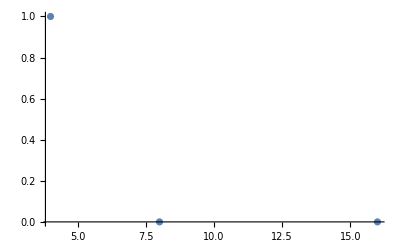

```mathematica
(*Graficar probabilidad de cada posible orden estimado*)
L1
ListPlot[L1]
```

{{1,(8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8)))/(1/2+8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4))+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8)))},{1,(8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4)))/(1/2+8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4))+(8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8)))/(1/2+8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4))+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8))))},{5,1/(2 (1/2+(8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8)))/(1/2+8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4))+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8)))+(8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4)))/(1/2+8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4))+(8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8)))/(1/2+8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4))+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8))))))}}

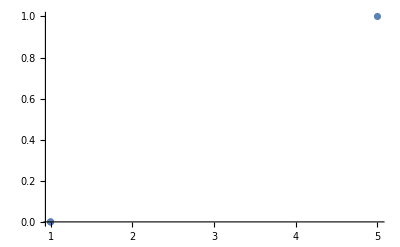

{{15,(8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8)))/(1/2+8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4))+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8)))},{15,(8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4)))/(1/2+8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4))+(8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8)))/(1/2+8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4))+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8))))},{3,1/(2 (1/2+(8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8)))/(1/2+8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4))+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8)))+(8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4)))/(1/2+8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4))+(8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8)))/(1/2+8 (1/16 ⅇ^(-(ⅈ π)/4)+1/16 ⅇ^((ⅈ π)/4)+1/16 ⅇ^(-(3 ⅈ π)/4)+1/16 ⅇ^((3 ⅈ π)/4))^2+8 (1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)) (1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4))+16 (1/16 ⅇ^((ⅈ π)/8)+1/16 ⅇ^(-(3 ⅈ π)/8)+1/16 ⅇ^((5 ⅈ π)/8)+1/16 ⅇ^(-(7 ⅈ π)/8)) (1/16 ⅇ^(-(ⅈ π)/8)+1/16 ⅇ^((3 ⅈ π)/8)+1/16 ⅇ^(-(5 ⅈ π)/8)+1/16 ⅇ^((7 ⅈ π)/8))))))}}

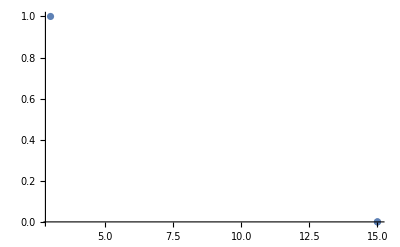

```mathematica
(*Graficar la probabilidad de cada posible factorización hallada*)
L2
ListPlot[L2]
L3
ListPlot[L3]
```

```mathematica
psipy={{3.24431432*^-02-2.11019772*^-02I},{1.02238627*^-01+1.24186877*^-01I},{-1.45872508*^-02+4.96195402*^-03I},{-7.81068904*^-03+7.09523404*^-03I},{7.89289508*^-02+1.97589772*^-01I},{-1.74289260*^-02-6.61375235*^-04I},{-1.66469627*^-02+3.29708049*^-02I},{-7.98806725*^-03+5.22655053*^-03I},{-2.65665129*^-02+9.93207704*^-03I},{2.72681717*^-01+5.71253089*^-02I},{4.82214712*^-03+1.10914123*^-02I},{2.47704819*^-03+1.76146365*^-02I},{-5.73127575*^-03+9.45364516*^-03I},{1.74563760*^-03+1.90200848*^-02I},{1.67259537*^-01-2.30814665*^-02I},{-2.24126180*^-03+3.48766354*^-03I},{4.41642019*^-03+2.18451914*^-02I},{-5.80938172*^-02-1.17904207*^-02I},{2.65251042*^-03-5.24678821*^-03I},{-2.26521884*^-03-7.29353557*^-03I},{-4.93872898*^-02-5.07250577*^-02I},{1.20899822*^-02-9.78980372*^-03I},{1.52013976*^-02-1.42193034*^-02I},{-2.73932038*^-03-1.20902479*^-03I},{1.47753762*^-02+2.15513493*^-03I},{-9.38437851*^-02-6.06473173*^-02I},{2.21025588*^-03-7.32968668*^-03I},{3.36388018*^-03-1.38997208*^-02I},{7.20764199*^-03-2.08755256*^-03I},{1.20895844*^-03-4.65499102*^-03I},{-2.59213299*^-02-8.07315917*^-02I},{-5.29979789*^-03-8.99123224*^-03I},{7.84008183*^-03+2.81311848*^-03I},{-5.85863830*^-02-3.40458264*^-02I},{6.11675268*^-04-9.65960619*^-04I},{1.40205268*^-04-4.07909503*^-03I},{2.10364419*^-05+1.29817745*^-03I},{2.95498593*^-03+1.19362151*^-03I},{1.35713901*^-03-4.50325557*^-04I},{3.26442441*^-03+1.77182351*^-03I},{7.91816112*^-04+3.91951975*^-03I},{-1.30147863*^-02-4.78718682*^-03I},{1.07890983*^-03-6.37235340*^-03I},{-1.66899547*^-03-4.15538038*^-03I},{6.19561748*^-03-5.55077986*^-04I},{2.33533008*^-04-1.53531579*^-03I},{-5.70778698*^-02-5.88743301*^-02I},{3.71172112*^-03-1.82633029*^-04I},{1.74692822*^-03-1.88658529*^-02I},{-1.25335029*^-02-6.17552570*^-02I},{-4.68834126*^-03+4.48119124*^-04I},{3.04165295*^-03+5.22675219*^-04I},{8.94724706*^-02+5.34445807*^-02I},{-3.07136185*^-03+5.40117622*^-03I},{-5.31108660*^-03+7.31560766*^-03I},{6.41061140*^-03+6.22118295*^-03I},{-5.52459320*^-03-1.58815760*^-03I},{2.19972441*^-02+9.24437489*^-02I},{4.12710613*^-03-3.46505576*^-03I},{-4.28237158*^-03-3.48443275*^-04I},{5.09409735*^-03+5.53835820*^-03I},{-4.46491415*^-03+3.30492700*^-03I},{-4.10479621*^-02-2.47476631*^-02I},{1.21789810*^-02+1.27782420*^-03I},{-2.39899333*^-02-3.27997485*^-04I},{1.00954532*^-01+1.19728506*^-01I},{1.28190993*^-02-1.83356551*^-03I},{-8.14937348*^-03+9.65545937*^-03I},{-7.53773282*^-02-1.95097027*^-01I},{3.35479599*^-03-9.55414844*^-03I},{1.61872740*^-02-1.64045104*^-02I},{-2.99261777*^-03+1.42397143*^-03I},{1.62911122*^-02+2.02219483*^-02I},{5.16435561*^-02-2.70750026*^-01I},{-6.30330690*^-03+9.33537976*^-03I},{1.52994212*^-02-1.28782400*^-03I},{-4.31392447*^-03-7.86590476*^-03I},{1.33725767*^-02-2.37420551*^-03I},{2.34188670*^-02+1.70079621*^-01I},{-5.92290964*^-03+1.99037876*^-02I},{1.78999749*^-03-1.27558796*^-02I},{-6.12507886*^-02-1.15077600*^-02I},{-2.86051274*^-03+3.88692057*^-03I},{-2.96213243*^-03-8.52199708*^-03I},{4.84337101*^-02+5.28657517*^-02I},{1.02534673*^-03+6.85537087*^-03I},{-3.56407034*^-03+1.39478459*^-02I},{-1.96323756*^-03-3.70896419*^-03I},{-1.31786668*^-02-6.60857674*^-03I},{-5.75942374*^-02+9.04335199*^-02I},{3.86320447*^-03+1.89986774*^-03I},{-1.19803203*^-02-4.12834900*^-03I},{1.22946498*^-03+7.66719965*^-03I},{-4.25852691*^-03+4.51304547*^-04I},{7.83158224*^-02-2.74467476*^-02I},{-1.02448158*^-03-8.08967470*^-03I},{-5.69865622*^-03+8.07414730*^-03I},{-5.80881209*^-02-3.40693675*^-02I},{-6.04158211*^-05+4.70102169*^-04I},{-1.67746746*^-04-3.26756981*^-03I},{-1.89527659*^-03-3.75576220*^-04I},{7.41312604*^-04-5.38172541*^-04I},{2.20728488*^-03-4.32021665*^-03I},{-5.12912274*^-04-1.04847579*^-04I},{3.43387446*^-04-4.20872604*^-03I},{-2.33072833*^-03+7.81405261*^-03I},{5.26095129*^-03+1.27777405*^-03I},{-2.98608640*^-03-7.24923300*^-04I},{1.92726164*^-03+4.69234001*^-03I},{-2.33686130*^-03+1.71322340*^-03I},{5.99449625*^-02-5.80664204*^-02I},{-1.92347336*^-03+9.13764348*^-03I},{-3.17452340*^-03+1.42943206*^-02I},{-8.97880238*^-03-6.09778297*^-02I},{3.55662411*^-03-1.05045156*^-04I},{2.36781537*^-03+2.09125248*^-03I},{-9.25853172*^-02-5.45889433*^-02I},{-2.91675529*^-03+7.32837080*^-03I},{5.26278318*^-03-1.72292993*^-02I},{1.05355035*^-03+4.36032149*^-03I},{-5.32322899*^-03+3.38978342*^-03I},{9.54100320*^-02-2.38335421*^-02I},{3.82165673*^-03+1.48612259*^-03I},{1.13276978*^-03+4.41412712*^-04I},{-5.47328332*^-03+2.09339193*^-03I},{1.05345980*^-03+3.52358951*^-03I},{2.74635006*^-02-4.15962646*^-02I},{8.06728868*^-03+1.37578465*^-02I},{2.21006496*^-02-1.22035463*^-02I},{1.00590082*^-01+1.13151451*^-01I},{-8.03277421*^-03+6.60826171*^-04I},{-8.23236320*^-03+6.93019472*^-03I},{7.69967614*^-02+1.94126036*^-01I},{-1.39725194*^-02-3.45444977*^-03I},{-3.31670789*^-02+1.20125997*^-02I},{-1.47675880*^-03+6.72546321*^-03I},{1.11744921*^-02-2.15371439*^-02I},{-2.75556248*^-01-4.75415805*^-02I},{-6.17480692*^-03-5.60149427*^-03I},{-4.49127827*^-03-2.00237314*^-02I},{7.11954991*^-04+3.24414788*^-05I},{-3.27004197*^-03-1.65557707*^-02I},{-1.72070587*^-01+2.54405633*^-02I},{-2.20414612*^-02+4.97103595*^-03I},{7.39300689*^-04+1.88552953*^-02I},{-5.97720216*^-02-5.51417593*^-03I},{9.70385586*^-04-3.31119091*^-03I},{-4.08082684*^-03-6.79847854*^-03I},{-4.93468777*^-02-5.10662906*^-02I},{1.09579874*^-02-8.75123556*^-03I},{4.66769126*^-03-1.22227076*^-03I},{3.16353214*^-03-4.30160008*^-03I},{1.36629002*^-03+4.60393490*^-03I},{9.81955357*^-02+5.74190311*^-02I},{-2.91957524*^-03+5.13310366*^-03I},{-4.44502966*^-03+1.04568377*^-02I},{-4.94029015*^-03+3.74081065*^-04I},{-2.79955766*^-03+3.86883993*^-03I},{2.93358784*^-02+7.79345261*^-02I},{-2.32205832*^-03+3.43439129*^-03I},{1.14651901*^-02+2.98044773*^-03I},{-5.83128633*^-02-3.40070932*^-02I},{-1.19695852*^-03+8.11533952*^-04I},{-5.78893484*^-04-3.25730034*^-03I},{1.14475775*^-03+1.70412251*^-03I},{2.64845757*^-03+8.42087983*^-04I},{2.70234197*^-03+8.78696485*^-03I},{-4.45413269*^-04-3.35088272*^-03I},{6.35519433*^-04-2.78831134*^-03I},{1.26018100*^-02+3.02467697*^-03I},{-2.62947646*^-03+4.82693195*^-03I},{-3.49804439*^-04+5.10897988*^-04I},{-4.50990228*^-03+4.02218991*^-03I},{1.28631269*^-03+6.83154718*^-04I},{5.72104637*^-02+6.05879948*^-02I},{-8.58485785*^-03-6.61632394*^-05I},{-4.50108591*^-03-1.66532739*^-02I},{-9.68803171*^-03-6.43437722*^-02I},{-5.38854386*^-03+4.59682206*^-03I},{1.66753699*^-03+1.73262288*^-03I},{8.88747537*^-02+5.52416411*^-02I},{-1.88547798*^-03+3.36643404*^-03I},{5.43270829*^-03+1.82955577*^-02I},{3.20408091*^-03-6.97924334*^-04I},{6.27047705*^-03-2.81294521*^-03I},{-2.26862305*^-02-9.32823032*^-02I},{-2.50176843*^-03+9.75975625*^-04I},{2.83075060*^-03-2.78653034*^-03I},{-1.12811546*^-03-1.97393218*^-03I},{4.22024913*^-03-1.27919654*^-03I},{4.16686348*^-02+2.62433598*^-02I},{-3.20388258*^-04+6.81494960*^-03I},{-1.54549534*^-02+9.00110519*^-03I},{9.33394937*^-02+1.22034567*^-01I},{1.07893904*^-02-7.71254449*^-03I},{-7.31670989*^-03+5.00517107*^-03I},{-7.65493962*^-02-1.97449248*^-01I},{3.31024250*^-03-7.57087326*^-03I},{3.34153963*^-02-2.99924577*^-02I},{-4.40298768*^-03+1.09014353*^-02I},{-1.17082324*^-02-7.71347740*^-03I},{-5.42704223*^-02+2.81920363*^-01I},{1.08901518*^-02-4.52191778*^-03I},{-1.74616223*^-02-1.02630300*^-03I},{7.23260034*^-03-4.21595374*^-03I},{-1.66926122*^-02-3.68845781*^-04I},{-2.39170831*^-02-1.70350605*^-01I},{-1.92727730*^-02-1.65141675*^-02I},{-1.18730122*^-03-9.15949956*^-03I},{-5.78451488*^-02-1.01749602*^-02I},{-5.73292543*^-04+4.95599595*^-03I},{-4.08155568*^-03-5.57019023*^-03I},{5.04031200*^-02+5.00932827*^-02I},{-6.90578359*^-05+6.93723783*^-03I},{-1.56019547*^-02+1.81805101*^-03I},{3.87874031*^-04-2.27350645*^-03I},{1.53182012*^-03+5.36556080*^-03I},{6.00372775*^-02-9.67703434*^-02I},{-8.27421768*^-03-1.41455344*^-03I},{9.72166999*^-03-4.65322885*^-04I},{-3.00749938*^-03-4.87725473*^-03I},{7.37923547*^-03-1.17441616*^-04I},{-7.96997041*^-02+2.80432157*^-02I},{-2.92756263*^-03-3.52415805*^-03I},{-5.57505441*^-03+3.94341463*^-03I},{-5.93459791*^-02-3.46223057*^-02I},{5.33027210*^-04+4.04467575*^-04I},{-2.18824918*^-04-3.92018701*^-03I},{-1.83374798*^-03-1.52857641*^-03I},{1.53624424*^-03-6.66747407*^-04I},{-6.60545079*^-03-4.05926329*^-03I},{3.44990530*^-03-2.09768402*^-03I},{4.40244428*^-03-4.95469876*^-03I},{2.58094818*^-03-1.43892521*^-02I},{-5.85073523*^-03-2.18460239*^-03I},{1.76126870*^-03-3.74818277*^-03I},{-3.65903160*^-03-7.08193873*^-03I},{3.40411913*^-03-1.23530951*^-03I},{-5.99058307*^-02+5.60276664*^-02I},{-2.10162474*^-03-6.66487765*^-03I},{6.48087757*^-05+2.17214568*^-02I},{-1.08346385*^-02-6.29203556*^-02I},{6.08863661*^-03-2.68853888*^-03I},{2.37015713*^-03+3.80237773*^-04I},{-9.06176305*^-02-5.46590356*^-02I},{-9.76805593*^-04+6.95795453*^-03I},{-6.26861470*^-03-8.26105855*^-03I},{8.26188576*^-03+1.19453724*^-04I},{5.09341614*^-03+7.33449275*^-04I},{-9.40447313*^-02+2.18603144*^-02I},{-1.00479960*^-03-4.19215444*^-03I},{-1.77228154*^-03-4.08992470*^-03I},{2.55274868*^-03-5.60714147*^-03I},{-6.45623812*^-05-3.50909192*^-03I},{-2.30383647*^-02+4.15708464*^-02I},{4.40610948*^-03-5.87936195*^-03I}};
```

```mathematica
Abs[psipy†.ψt]
```

{{0.363599}}

```mathematica
Table[{i/2^4,Subscript[ψt, i][[1,1]]},{i,0,15}]//N
```

{{0.,0.25},{0.0625,1.92593×10^-34+0. ⅈ},{0.125,7.70372×10^-34+0. ⅈ},{0.1875,1.92593×10^-34+0. ⅈ},{0.25,0.25},{0.3125,1.92593×10^-34+0. ⅈ},{0.375,7.70372×10^-34+0. ⅈ},{0.4375,1.92593×10^-34+0. ⅈ},{0.5,0.25},{0.5625,1.92593×10^-34+0. ⅈ},{0.625,7.70372×10^-34+0. ⅈ},{0.6875,1.92593×10^-34+0. ⅈ},{0.75,0.25},{0.8125,1.92593×10^-34+0. ⅈ},{0.875,7.70372×10^-34+0. ⅈ},{0.9375,1.92593×10^-34+0. ⅈ}}

```mathematica
psipy8={{2.58671981*^-02+7.34682219*^-03I},{-1.70565921*^-01+2.70949502*^-01I},{7.38509561*^-03+1.62063372*^-02I},{1.74660746*^-01+1.32522679*^-01I},{-5.37293002*^-03-1.47461251*^-02I},{-8.74372942*^-02+8.24359355*^-02I},{-1.31128247*^-02+9.30655052*^-03I},{3.53546422*^-02+1.95416229*^-02I},{-3.76172407*^-03-4.55759595*^-03I},{-2.34588212*^-02-9.35007457*^-03I},{6.73250894*^-03+2.06066843*^-03I},{1.36873548*^-02+6.66166912*^-03I},{8.98243107*^-04+7.79406399*^-04I},{-3.62553478*^-03-2.42204929*^-03I},{8.73114381*^-04-3.44480680*^-03I},{3.96952699*^-04+2.92252432*^-03I},{-8.87606561*^-03+1.26934507*^-02I},{5.17662734*^-02-1.54184995*^-01I},{1.02738337*^-02-9.58145370*^-03I},{-4.80174047*^-02-1.83496607*^-01I},{5.64666060*^-04+1.15469129*^-02I},{1.06176825*^-02+7.99462876*^-04I},{6.86348687*^-04+6.53679567*^-03I},{7.52444830*^-03-2.41437614*^-02I},{-1.05348261*^-02+4.31039190*^-03I},{2.85332148*^-02+7.50965010*^-03I},{-5.91281941*^-03+1.23565263*^-03I},{-6.53545402*^-04-9.32157135*^-03I},{-6.83447303*^-03-3.41808543*^-03I},{1.78989815*^-03+2.37073670*^-03I},{-4.57770794*^-03-1.71236750*^-03I},{-5.01283071*^-03-8.56289741*^-03I},{-1.05780569*^-03+5.05134728*^-03I},{4.32052360*^-02-7.55104906*^-02I},{2.08093835*^-03-9.54318849*^-03I},{5.99467945*^-02-4.34678907*^-02I},{4.69681715*^-03-2.02186451*^-03I},{3.27871300*^-02-5.45342676*^-02I},{1.06133850*^-02-1.00917908*^-02I},{3.15264359*^-02-2.55375687*^-02I},{-1.78739699*^-03-1.40152989*^-02I},{-1.85583282*^-02+6.19005743*^-04I},{3.60829930*^-04-3.17751215*^-03I},{-5.43324232*^-03-5.17264570*^-03I},{2.72898611*^-03-3.65590769*^-03I},{-2.61078684*^-03-1.19944260*^-03I},{-1.79790905*^-03+3.00255326*^-03I},{-5.86958197*^-04+1.57335697*^-03I},{-6.56551451*^-03-2.77876118*^-02I},{-4.12472551*^-02+1.84310924*^-01I},{-1.71100218*^-02+3.44184500*^-03I},{-1.07607987*^-01+1.09884493*^-01I},{-6.57806397*^-03-8.25412229*^-03I},{-4.36809203*^-02+7.78001961*^-02I},{-1.12245296*^-02+8.67636294*^-03I},{-1.02046659*^-02+2.83725421*^-02I},{1.48062728*^-02+1.19095163*^-03I},{-2.44156962*^-03-1.19065314*^-03I},{2.44149079*^-03-7.23218049*^-04I},{-4.23586846*^-03+3.19077027*^-03I},{2.02457239*^-03-4.76682765*^-04I},{-2.95284937*^-04-1.90548527*^-04I},{3.44341573*^-03+1.19254027*^-03I},{2.85194002*^-03+6.58511822*^-03I},{-1.59037132*^-02+1.23715669*^-02I},{8.00628129*^-02-1.21707134*^-01I},{3.64598777*^-03+7.09004859*^-03I},{1.45728323*^-01-1.60240389*^-01I},{6.30450140*^-03+4.04407377*^-03I},{4.46121591*^-02-2.53192387*^-02I},{4.39157318*^-03-6.70061730*^-03I},{5.22678587*^-02-4.09487170*^-02I},{-8.66159155*^-03+4.25061189*^-03I},{8.34437824*^-03-3.28280562*^-03I},{-2.83903333*^-03+8.42091047*^-04I},{4.96816214*^-03-5.00637099*^-03I},{-2.09009466*^-03-1.86419840*^-04I},{2.35932561*^-03-7.66762964*^-04I},{8.52324001*^-04-9.86731106*^-04I},{8.86374039*^-03-4.46163256*^-03I},{2.26511541*^-02-2.90837503*^-03I},{-1.35810542*^-01+6.31968246*^-02I},{-4.31293682*^-03+4.29374900*^-03I},{-1.01992238*^-01+9.96817659*^-02I},{6.18649705*^-03-1.05415598*^-02I},{-4.21176811*^-02-4.92854370*^-03I},{-3.13581185*^-03+1.07375093*^-03I},{-6.41880428*^-03+1.07936671*^-02I},{-2.14435390*^-03-1.16927092*^-02I},{-6.66660630*^-03-8.26117472*^-03I},{2.14227478*^-03+3.94301624*^-03I},{-1.61160408*^-03+3.42596096*^-03I},{1.78036989*^-03-9.34341263*^-04I},{-3.21427030*^-04-2.02773544*^-04I},{-5.89710625*^-06-1.59129669*^-04I},{-3.89568284*^-03+3.49362830*^-03I},{-2.19057688*^-02-9.33727120*^-03I},{4.03735962*^-02-1.29746254*^-02I},{-1.69046327*^-03+1.00098691*^-02I},{4.67046829*^-02-7.51212377*^-02I},{-7.91054542*^-03+5.49134464*^-03I},{-1.79249154*^-02+2.82576035*^-02I},{-1.51217105*^-02+2.03217924*^-03I},{1.81908019*^-02-1.57291288*^-02I},{9.12428970*^-03+6.13038720*^-04I},{1.25037341*^-02+1.81289172*^-02I},{-1.23575095*^-03-2.20428726*^-03I},{9.31383861*^-04+5.19318139*^-05I},{1.94061878*^-03-3.44606832*^-03I},{-5.49909833*^-04+1.60327549*^-03I},{1.03144686*^-03-2.13424039*^-03I},{2.97045384*^-03-2.87179794*^-03I},{2.82777015*^-04-1.34991458*^-03I},{1.15216217*^-01-9.90494202*^-02I},{2.67397666*^-02-1.58453164*^-03I},{1.77573549*^-01+8.44015969*^-03I},{-3.15067377*^-03-3.04395422*^-03I},{5.81415975*^-02-4.16200139*^-02I},{2.13505001*^-02+5.35146316*^-03I},{5.42099141*^-02-1.03765962*^-02I},{6.65008265*^-03-3.85554112*^-03I},{-9.34029025*^-03-8.95134097*^-03I},{1.16622582*^-03-2.18325462*^-03I},{7.89992081*^-03-4.16011671*^-03I},{3.80176772*^-03+1.96015880*^-03I},{-2.89416931*^-04-1.37428174*^-03I},{-3.93768539*^-03-1.49029213*^-03I},{2.44914648*^-03-3.71468778*^-03I},{3.19890300*^-02+9.03863866*^-03I},{-1.18662093*^-01+2.10861440*^-01I},{-2.08055542*^-02-2.13751783*^-02I},{-2.53079482*^-01-1.53545197*^-01I},{6.82992953*^-03-5.48632906*^-03I},{-4.95786752*^-02+7.39684056*^-02I},{-1.01244676*^-02+2.38929772*^-03I},{-3.33898234*^-02-2.46461402*^-02I},{-2.70719969*^-03+9.56537753*^-03I},{-6.94534569*^-03+2.78950992*^-03I},{2.26435236*^-03+1.46509685*^-03I},{-1.22138280*^-02-9.32594969*^-03I},{1.38883860*^-03+2.43319029*^-03I},{-1.89347823*^-03+1.30468606*^-03I},{-2.95706296*^-05+5.37092265*^-03I},{-7.65812591*^-03+9.09168598*^-04I},{-2.34919077*^-02+1.53099034*^-02I},{1.14134611*^-02-1.42718048*^-01I},{-1.81133742*^-02+1.65266314*^-02I},{1.42537287*^-01+1.04720748*^-01I},{1.91958371*^-03+7.22491776*^-03I},{9.96852495*^-03-1.78420011*^-02I},{-3.20831551*^-04-1.16327886*^-02I},{5.13791825*^-02+5.85623695*^-03I},{3.31614144*^-03+1.84608383*^-03I},{1.89829002*^-02-1.01917279*^-04I},{-3.55769235*^-03+1.23021555*^-03I},{1.50256699*^-03+8.08527369*^-03I},{-2.30494315*^-03-1.38069286*^-04I},{3.93928814*^-03+1.00989897*^-03I},{3.80788989*^-03+9.21221657*^-04I},{4.13445383*^-03-1.53783294*^-03I},{8.07600970*^-03+1.61837226*^-02I},{2.35316381*^-02-8.87652012*^-02I},{1.42558694*^-02+1.29102238*^-02I},{-3.14568644*^-02-1.21204768*^-02I},{1.70577298*^-03-1.04966957*^-02I},{1.32349119*^-02-5.99514898*^-02I},{-7.04526153*^-04+7.49385880*^-03I},{7.92134806*^-03-1.02152658*^-02I},{3.03752462*^-04-9.55963810*^-03I},{-9.73868085*^-03-2.59071997*^-03I},{-2.08487019*^-04+3.88296039*^-04I},{1.58937857*^-03+1.22157460*^-03I},{2.07893266*^-03+1.47380152*^-03I},{-2.49134567*^-03-1.50400706*^-03I},{9.31795990*^-04-4.25350703*^-03I},{4.10073891*^-03-1.31847248*^-03I},{-3.69381313*^-03-2.47191430*^-02I},{3.66944818*^-04+2.14503185*^-01I},{-1.47647044*^-03-6.43127186*^-03I},{8.16116969*^-02-1.16009967*^-01I},{-1.02886114*^-02+3.27651979*^-04I},{-2.53126617*^-02+9.60252449*^-02I},{-6.86630846*^-03+1.98550506*^-03I},{2.76651968*^-02-2.27192414*^-02I},{7.31571655*^-03+8.68418420*^-03I},{-1.28727339*^-02+1.08312744*^-02I},{3.55809454*^-03-1.61311562*^-03I},{4.32726790*^-03-9.22893660*^-03I},{3.23608227*^-03+1.27622148*^-03I},{-1.76329274*^-03+1.43126062*^-04I},{-1.59823613*^-03-3.24679546*^-04I},{-2.63310166*^-03-1.33453708*^-03I},{-4.58833964*^-03+5.87398570*^-03I},{4.94013386*^-02-1.58409260*^-01I},{1.76007147*^-03+6.91144107*^-03I},{-5.52852656*^-02+8.29850406*^-02I},{5.73813049*^-03-2.53028474*^-03I},{3.81024730*^-02-4.02090913*^-02I},{6.87391338*^-03+4.58042094*^-03I},{1.47874723*^-02+1.50641595*^-02I},{-1.38562245*^-03+1.62843382*^-02I},{1.89688966*^-02-1.61896431*^-02I},{-3.35168857*^-04+2.71401305*^-03I},{-2.62853119*^-03+3.62671893*^-03I},{-4.11204711*^-03+5.35988341*^-03I},{3.45121361*^-03-5.86415285*^-04I},{-1.01786551*^-03+5.13822035*^-04I},{-7.24268251*^-04-5.77550983*^-05I},{1.92588129*^-02+1.07929893*^-02I},{-1.04600009*^-01+8.49313499*^-02I},{6.23987046*^-03-8.57995702*^-03I},{6.18826515*^-02-1.50316685*^-01I},{4.43794434*^-03-4.65993964*^-03I},{-4.35984207*^-02+8.97487000*^-03I},{-7.32914818*^-03+1.19036826*^-03I},{1.91752491*^-02-3.65143888*^-02I},{-1.28265670*^-02-1.25528676*^-02I},{-1.29630696*^-02+3.61268885*^-03I},{4.07874998*^-04-6.29983159*^-04I},{1.49618729*^-03-6.59982256*^-03I},{-1.56711218*^-03-1.83856420*^-03I},{-2.13166362*^-03+4.86206767*^-04I},{-1.01888809*^-03+1.19680869*^-03I},{7.08568188*^-04+1.73247518*^-03I},{-1.58735817*^-02-1.78455531*^-02I},{3.45902506*^-02-8.24175869*^-03I},{-1.50328398*^-02-1.01015827*^-02I},{4.94540351*^-03+3.51674977*^-02I},{-8.62061780*^-03+7.87064033*^-03I},{-5.08276090*^-03+4.82057342*^-02I},{5.82548926*^-03-1.39063073*^-03I},{2.31452098*^-02+1.74332661*^-02I},{3.76928601*^-03+5.69870512*^-03I},{1.11738377*^-02+8.61209963*^-03I},{-3.33816081*^-03-6.11076903*^-04I},{-2.88135239*^-03+2.16768865*^-04I},{-1.24637809*^-03-3.95453966*^-04I},{6.62522211*^-04+2.89103661*^-03I},{-1.21351917*^-04+1.70294629*^-03I},{1.69915936*^-03-1.51873651*^-03I},{-2.22108274*^-03+6.69651157*^-03I},{1.36998967*^-01-1.52452432*^-01I},{-7.94120997*^-03+1.47626559*^-02I},{-1.00936786*^-01-6.44816178*^-02I},{1.06355892*^-02-7.97303152*^-03I},{7.60597430*^-02-7.48722446*^-02I},{-1.53095164*^-03-6.66681752*^-03I},{3.96527634*^-03-2.78032312*^-02I},{4.99803756*^-04+3.74131990*^-03I},{2.23594839*^-03-3.17224151*^-04I},{-9.55643805*^-04-6.91575956*^-04I},{-7.41377292*^-03-1.90694597*^-03I},{-2.13011740*^-03+1.05810096*^-03I},{1.47252824*^-03-6.36938453*^-04I},{3.76864501*^-03+1.24954718*^-04I},{1.72448925*^-03-2.32100694*^-03I}};
```

```mathematica
Abs[psipy8†.ψt]
```

{{0.390136}}